# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/pcs/Desktop/Entropy/Calculations/T1 positive parity/T1 FINAL/QMB_offline.wl"];
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

```mathematica
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

# T1

```mathematica
L=10;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
h=0.4;
g=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
```

```mathematica
La=L/2;
Lb=L-La;
eigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,newall[[All,2]]},DistributedContexts->Full];
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
```

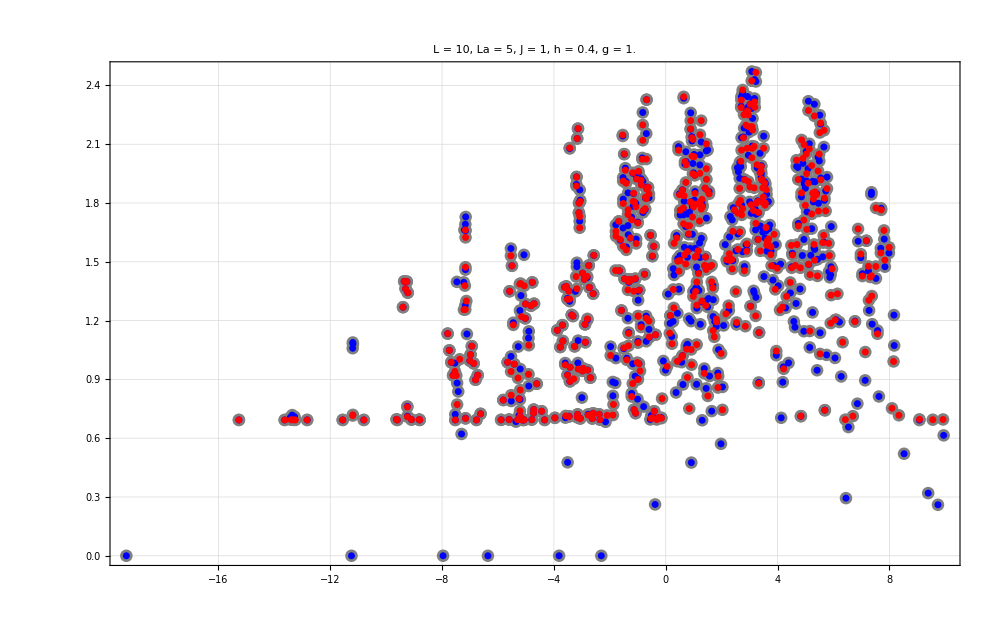

```mathematica
ListPlot[{Transpose[{newall[[All,1]],eigenvecdiag}],Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Gray,PointSize[0.009]],Directive[Blue,PointSize[0.005]],Directive[Red,PointSize[0.005]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]]
```

## Product state in positive sector

```mathematica
Peven=(1/2)(IdentityMatrix[2^L]+R);
```

```mathematica
productstates={};
Do[
allstates={};
Do[
a=Table[RandomQubitState[],L/2];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@a],Flatten[KroneckerProduct@@Reverse[a]]]];
AppendTo[allstates,evenini];
,{i,1000}];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,allstates}],First];
AppendTo[productstates,data[[1,2]]];
,{j,10}];
```

```mathematica
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,productstates},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,productstates}],First];
```

```mathematica
tlist=Table[10^i,{i,-1,4,0.0025}];
tlist//Length
```

2001

```mathematica
svntproduct=ParallelTable[{t,svn[L,La,Lb,j,allvals,allvecs,t]},{j,productstates},{t,tlist},DistributedContexts->Full];
```

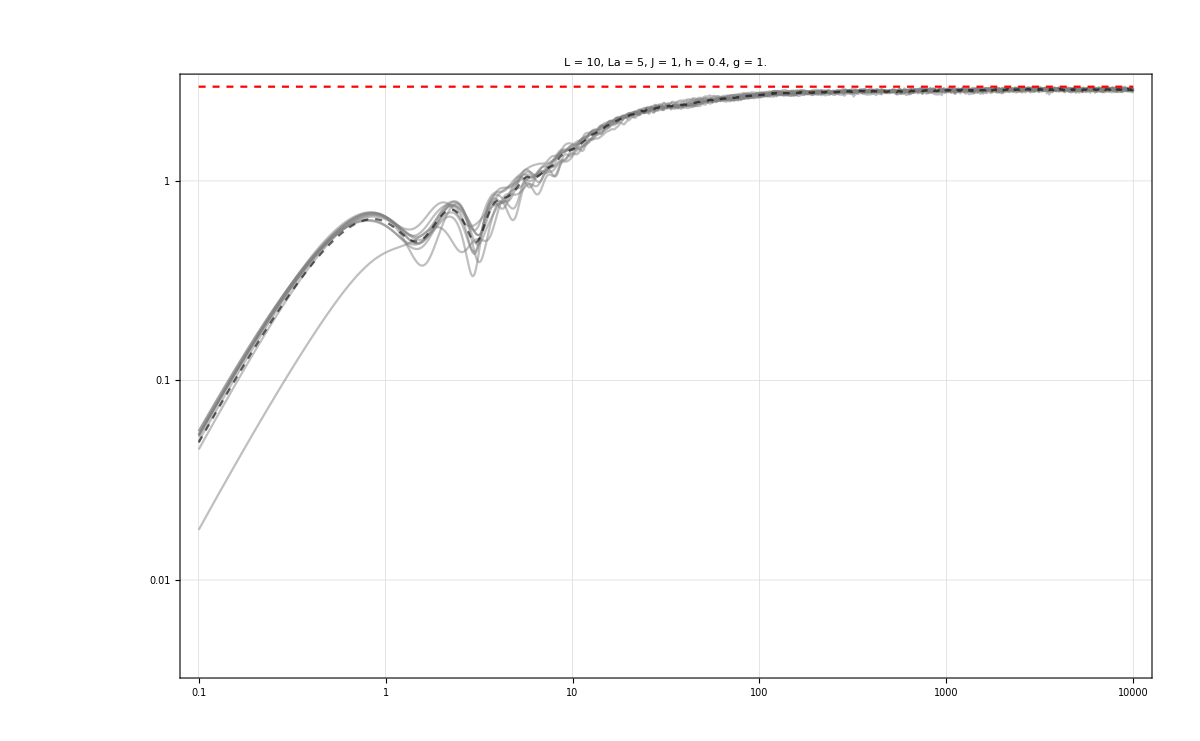

```mathematica
plot2=Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0,3}},Joined->True,PlotStyle->Directive[Gray,Opacity[0.5]],ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["+ RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

```mathematica
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
Transpose[{1/data[[All,1]],t1s,limits}]//TableForm
```

284.035 | 836.566 | 2.89942
259.871 | 278.612 | 2.89078
257.475 | 595.662 | 2.88592
250.907 | 841.395 | 2.84832
249.093 | 737.055 | 2.869
241.369 | 860.994 | 2.86806
240.958 | 649.382 | 2.87971
240.293 | 794.328 | 2.81346
237.669 | 258.523 | 2.84611
229.791 | 363.078 | 2.87524

```mathematica
energydifs=Sort[DeleteDuplicates[Flatten[ParallelTable[Chop[Abs[i-j]],{i,eveneigenval},{j,eveneigenval},DistributedContexts->Full]]]];
```

```mathematica
energydifs[[-1]]
tb=1/(4*energydifs[[-1]])
Max[t1s]/tb
```

29.2334

0.00855186

100679.